Below imports all the functions in toolbox.wl and gives a list of all those functions for you to use as a reference

```mathematica
filePath =ParentDirectory[NotebookDirectory[]]<>"\\src\\toolbox.wl";
Import[filePath]
fileContents = Import[filePath,"text"];
Table[If[StringContainsQ[sub,":="],StringReplace[sub,":="~~___->""
], Nothing],{sub,StringSplit[fileContents]}]//MatrixForm
```

(Swap[state_,pair_]
noOverlap[pairs_]
PossibleSwaps[n_]
allSetsOfSwaps[n_]
PossibleCorrelation[state_]
StateGraph[n_,e_]
AdjacencyMatrixInEnergySubspaceforEnergy[n_,e_]
AdjacencyMatrixforEnergy[n_,e_]
FullAdjacencyMatrixCanonical[n_]
FullAdjacencyMatrixEnergyBasis[n_]
ClassEquivilent[s1_,s2_]
AllEquivilentVert[s_]
ClassEquivilentEdge[e1_,e2_]
AllEquivilentEdges[e1_]
ClassEquivilentStateGraph[n_,e_]
ReducedClassEquivilentStateGraph[n_,e_])

```mathematica
True &&False
```

False

-Graphics-

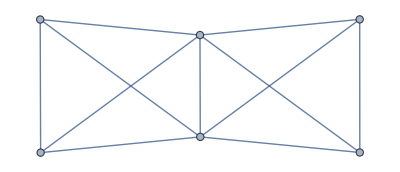

```mathematica
StateGraph[4,2]
SimpleGraph[UndirectedGraph[StateGraph[4,2]]]
```

```mathematica
ClassEquivilentStateGraph[8,2]
```

-Graphics-

Below is the method for producing the graphs we were drawing on the board.

```mathematica
G = ReducedClassEquivilentStateGraph[12,2]
```

-Graphics-

The above graph does have the “multiplicity” of each state. It is embedded in the VertexWeight attribute.

```mathematica
Table[s -> AnnotationValue[{G,s},VertexWeight],{s,VertexList[G]}]//MatrixForm
```

({1,1,0,0,0,0,0,0,0,0,0,0}→12
{1,0,1,0,0,0,0,0,0,0,0,0}→12
{0,0,1,0,0,0,0,0,0,0,0,1}→12
{0,0,0,1,0,0,0,0,0,0,0,1}→12
{0,0,0,0,1,0,0,0,0,0,0,1}→12
{0,0,0,0,0,1,0,0,0,0,0,1}→6)

```mathematica
ArrayPlot[AdjacencyMatrixInEnergySubspaceforEnergy[10,5],Mesh->"Nonzero"]
```

-Graphics-

```mathematica
M := AdjacencyMatrixInEnergySubspaceforEnergy[n,2];
Table[{n,Counts[Total[M]]},{n,2,10}]//MatrixForm
```

(2 | <|1→1|>
3 | <|3→3|>
4 | <|4→4,6→2|>
5 | <|4→5,8→5|>
6 | <|4→6,8→6,9→3|>
7 | <|4→7,8→7,9→7|>
8 | <|4→8,8→8,9→12|>
9 | <|4→9,8→9,9→18|>
10 | <|4→10,8→10,9→25|>)

```mathematica
ContainsQ
```

```mathematica
Mem
```

```mathematica
True&& 5
```

5

```mathematica
w = <|{1,1,0,0,0,0,0,0,0,0,0,0}->12,{1,0,1,0,0,0,0,0,0,0,0,0}->12,{0,0,1,0,0,0,0,0,0,0,0,1}->12,{0,0,0,1,0,0,0,0,0,0,0,1}->12,{0,0,0,0,1,0,0,0,0,0,0,1}->12,{0,0,0,0,0,1,0,0,0,0,0,1}->6|>
```

<|{1,1,0,0,0,0,0,0,0,0,0,0}→12,{1,0,1,0,0,0,0,0,0,0,0,0}→12,{0,0,1,0,0,0,0,0,0,0,0,1}→12,{0,0,0,1,0,0,0,0,0,0,0,1}→12,{0,0,0,0,1,0,0,0,0,0,0,1}→12,{0,0,0,0,0,1,0,0,0,0,0,1}→6|>

```mathematica
Normal[w]
```

{{1,1,0,0,0,0,0,0,0,0,0,0}→12,{1,0,1,0,0,0,0,0,0,0,0,0}→12,{0,0,1,0,0,0,0,0,0,0,0,1}→12,{0,0,0,1,0,0,0,0,0,0,0,1}→12,{0,0,0,0,1,0,0,0,0,0,0,1}→12,{0,0,0,0,0,1,0,0,0,0,0,1}→6}